```mathematica
DSolve[{x''[t]+2δ x'[t]+ω0^2 x[t]==0,x[0]==0,x'[0]==v},x[t],t]//FullSimplify
```

{{x[t]→(ⅇ^(-t δ) v Sinh[t √(δ^2-ω0^2)])/(√((δ-ω0) (δ+ω0)))}}

```mathematica
f[t_]:=v0/(√(ω0^2-δ^2))Sin[√(ω0^2-δ^2)t] ⅇ^(-δ t)
```

```mathematica
f''[t]+2δ f'[t]+ω0^2 f[t]//FullSimplify
```

0

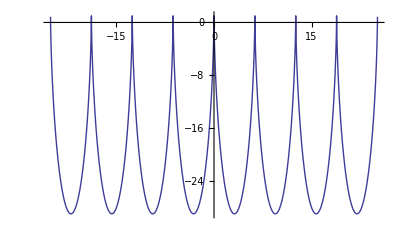

```mathematica
ParametricPlot[{t-Sin[t],1+15(Cos[t]-1)},{t,-25,25}]
```

```mathematica
DSolve[{(M+m)x''[t]==-q B y'[t],m y''[t]==-m g+q B x'[t],x[0]==x'[0]==y'[0]==0,y[0]==l},{x[t],y[t]},t]//FullSimplify
```

{{x[t]→(g m (B q t-√m √(m+M) Sin[(B q t)/(√m √(m+M))]))/(B^2 q^2),y[t]→(-g m (m+M)+B^2 l q^2+g m (m+M) Cos[(B q t)/(√m √(m+M))])/(B^2 q^2)}}